```mathematica
Get[FileNameJoin[{NotebookDirectory[],"GalaxyClassification.m"}]]
Needs["GalaxyClassification`"]
```

```mathematica
$VariableNames=Normal[$TrainingDataByID[1,Keys]]
```

{GalaxyID,C1S1,C1S2,C1S3,C2S1,C2S2,C3S1,C3S2,C4S1,C4S2,C5S1,C5S2,C5S3,C5S4,C6S1,C6S2,C7S1,C7S2,C7S3,C8S1,C8S2,C8S3,C8S4,C8S5,C8S6,C8S7,C9S1,C9S2,C9S3,C10S1,C10S2,C10S3,C11S1,C11S2,C11S3,C11S4,C11S5,C11S6}

```mathematica
allKeys=Normal[$TrainingDataByID[All,"GalaxyID"]];
```

```mathematica
$GalaxyImageSourceDirectory
$GalaxyImageFilteredDirectory
```

```mathematica
SystemOpen[$GalaxyImageSourceDirectory]
```

```mathematica
ClearAll[loadImageSource,loadImageFiltered,keyToImageSource,keyToImageFiltered];
loadImageSource[i_Integer,s_Integer]:=ImageResize[Import[FileNameJoin[{$GalaxyImageSourceDirectory,ToString[i]<>".jpg"}]],s]
loadImageFiltered[i_Integer,s_Integer]:=ImageResize[Import[FileNameJoin[{$GalaxyImageFilteredDirectory,ToString[i]<>".jpg"}]],s]
keyToImageSource[key_Integer,s_Integer]:=key->loadImageSource[key,s]
keyToImageFiltered[key_Integer,s_Integer]:=key->loadImageFiltered[key,s]
```

```mathematica
size=64;
```

```mathematica
DistributeDefinitions[loadImageSource,loadImageFiltered,keyToImageSource,keyToImageFiltered,GalaxyClassification`$GalaxyImageSourceDirectory]
```

{loadImageSource,$GalaxyImageSourceDirectory,loadImageFiltered,keyToImageSource,keyToImageFiltered}

```mathematica
If[FileExistsQ[FileNameJoin[{$ProjectDirectory,"imageLookupSource.mx"}]],
Get[FileNameJoin[{$ProjectDirectory,"imageLookupSource.mx"}]],
imageLookupSource=Association[ParallelMap[keyToImageSource[#,size]&,allKeys]];
DumpSave[FileNameJoin[{$ProjectDirectory,"imageLookupSource.mx"}],imageLookupSource];
];
```

```mathematica
If[FileExistsQ[FileNameJoin[{$ProjectDirectory,"imageLookupFiltered.mx"}]],
Get[FileNameJoin[{$ProjectDirectory,"imageLookupFiltered.mx"}]],
imageLookupFiltered=Association[ParallelMap[keyToImageFiltered[#,size]&,allKeys]];
DumpSave[FileNameJoin[{$ProjectDirectory,"imageLookupFiltered.mx"}],imageLookupFiltered];
];
```

```mathematica
SystemOpen[$ProjectDirectory]
```

```mathematica
ClearAll[sampleTrain,sampleTest];
sampleTrain=RandomSample[$TrainingDataByID,5000];
sampleTest=RandomSample[$TrainingDataByID,5000];
```

```mathematica
ClearAll[makeData];
makeData[sample_Dataset,imageLookupFunction_Association,label_String]:=Rule@@@Values/@Normal[sample[All,{"GalaxyID",label}]]/.i_Integer:>imageLookupFunction[i]
```

```mathematica
ClearAll[makeClassificationData];
makeClassificationData[sample_Dataset,imageLookupFunction_Association,label_String]:=makeData[sample,imageLookupFunction,label]/.v_Real:>v>0
```

```mathematica
s=RandomSample[sampleTrain,10];
makeData[s,imageLookupFiltered,"C1S2"]
makeClassificationData[s,imageLookupFiltered,"C1S2"]
```

{-Graphics-→1.33047,-Graphics-→-0.220902,-Graphics-→-0.693329,-Graphics-→-0.236456,-Graphics-→3.17805,-Graphics-→-0.067874,-Graphics-→3.99922,-Graphics-→-0.234266,-Graphics-→-0.543469,-Graphics-→2.39626}

{-Graphics-→True,-Graphics-→False,-Graphics-→False,-Graphics-→False,-Graphics-→True,-Graphics-→False,-Graphics-→True,-Graphics-→False,-Graphics-→False,-Graphics-→True}

```mathematica
ClearAll[trainingData,testData];

cf=#⟦1,1⟧->#⟦2,2⟧-#⟦1,2⟧>0&;

trainingData["C1S1","source"]=makeData[sampleTrain,imageLookupSource,"C1S1"];
trainingData["C1S2","source"]=makeData[sampleTrain,imageLookupSource,"C1S2"];
trainingData["C1S1","filtered"]=makeData[sampleTrain,imageLookupFiltered,"C1S1"];
trainingData["C1S2","filtered"]=makeData[sampleTrain,imageLookupFiltered,"C1S2"];

trainingData["classification","source"]=cf/@Transpose[{trainingData["C1S1","source"],trainingData["C1S2","source"]}];
trainingData["classification","filtered"]=cf/@Transpose[{trainingData["C1S1","filtered"],trainingData["C1S2","filtered"]}];

testData["C1S1","source"]=makeData[sampleTest,imageLookupSource,"C1S1"];
testData["C1S2","source"]=makeData[sampleTest,imageLookupSource,"C1S2"];
testData["C1S1","filtered"]=makeData[sampleTest,imageLookupFiltered,"C1S1"];
testData["C1S2","filtered"]=makeData[sampleTest,imageLookupFiltered,"C1S2"];

testData["classification","source"]=cf/@Transpose[{testData["C1S1","source"],testData["C1S2","source"]}];
testData["classification","filtered"]=cf/@Transpose[{testData["C1S1","filtered"],testData["C1S2","filtered"]}];
```

```mathematica
trainingData["classification","source"]⟦;;5⟧
```

{-Graphics-→False,-Graphics-→False,-Graphics-→True,-Graphics-→False,-Graphics-→True}

```mathematica
ClearAll[classify];

classify["source"]=Classify[trainingData["classification","source"],ValidationSet->testData["classification","source"],PerformanceGoal->"Quality"]
classify["filtered"]=Classify[trainingData["classification","filtered"],ValidationSet->testData["classification","filtered"],PerformanceGoal->"Quality"]
```

ClassifierFunction[…]

ClassifierFunction[…]

```mathematica
ClearAll[cm];
cm["source"]=ClassifierMeasurements[classify["source"],testData["classification","source"]]
cm["filtered"]=ClassifierMeasurements[classify["filtered"],testData["classification","filtered"]]
```

ClassifierMeasurements[…]

ClassifierMeasurements[…]

```mathematica
cm["source"]["Properties"]
```

{Accuracy,AccuracyRejectionPlot,ClassRejectionRate,ConfusionFunction,ConfusionMatrix,ConfusionMatrixPlot,Error,FScore,Likelihood,LogLikelihood,LogLikelihoodRate,Precision,Properties,Recall,RejectionRate}

```mathematica
cm["source"]["Accuracy"]
cm["filtered"]["Accuracy"]
```

0.776

0.7784

```mathematica
TableForm[Table[Row[{label,Spacer[10],type,Spacer[10],cm[label,type]["Accuracy"]}],{type,{"source","filtered"}},{label,{"C1S1","C1S2"}}]]
```

C1S1source0.754 | C1S2source0.751
C1S1filtered0.762 | C1S2filtered0.766

```mathematica
ClearAll[predict];

predict["C1S1","source"]=Predict[trainingData["C1S1","source"],ValidationSet->testData["C1S1","source"],Method->"LinearRegression"]
predict["C1S2","source"]=Predict[trainingData["C1S2","source"],ValidationSet->testData["C1S2","source"],Method->"LinearRegression"]

predict["C1S1","filtered"]=Predict[trainingData["C1S1","filtered"],ValidationSet->testData["C1S1","filtered"],Method->"LinearRegression"]
predict["C1S2","filtered"]=Predict[trainingData["C1S2","filtered"],ValidationSet->testData["C1S2","filtered"],Method->"LinearRegression"]
```

PredictorFunction[…]

PredictorFunction[…]

PredictorFunction[…]

«1 more identical outputs»

```mathematica
flipColor[fimg_Image]:=If[
With[{fimgData=ImageData[ColorConvert[fimg,"Grayscale"]]},
Mean[Join[
fimgData⟦All,1⟧,
fimgData⟦All,-1⟧,
fimgData⟦1,All⟧,
fimgData⟦-1,All⟧
]]>0.5
],
ColorNegate[fimg],
fimg
]

galaxyFilter[img_Image]:=Module[
{channels,kld,mask},
channels=ImageAdjust/@Join[
ColorSeparate[img,"RGB"],
ColorSeparate[img,"LUV"],
Table[GradientFilter[img,i],{i,0.5,8.0,0.25}],
Flatten[ColorSeparate/@Table[RidgeFilter[img,i],{i,1,3}]],
Flatten[Table[ColorSeparate[DifferentiatorFilter[img,w]],{w,0.15,0.45,0.1}]],
Flatten[Table[ColorSeparate/@Table[DerivativeFilter[img,{n,0},sigma],{sigma,0.25,1.75,0.25}],{n,2}]],
Flatten[Table[ColorSeparate/@Table[DerivativeFilter[img,{0,n},sigma],{sigma,0.25,1.75,0.25}],{n,2}]],
With[{n0=8},Flatten[Table[ColorSeparate/@Table[GaborFilter[img,r,{Cos[(n π)/n0],Sin[(n π)/n0]}],{n,n0}],{r,3,6,1}]]],
Flatten[ColorSeparate/@Table[LaplacianGaussianFilter[img,n],{n,3,8}]]
];
kld=flipColor/@(ImageAdjust/@First[KarhunenLoeveDecomposition[channels]]);
mask=ImageAdjust[GaussianFilter[Dilation[kld⟦1⟧,2],5]];
With[{p=1.0},
ColorCombine[{kld⟦1⟧,ImageMultiply[kld⟦2⟧,mask],ImageMultiply[Blend[kld⟦3;;⟧,With[{seq=Table[1/n^p,{n,Length[kld]-2}]},seq/Total[seq]]],mask]},"LUV"]
]
]
```

```mathematica
SortBy[test,Last]⟦-10;;⟧
```

{-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873,-Graphics-→72.0873}

```mathematica
DistributeDefinitions[galaxyFilter]
```

{galaxyFilter}

```mathematica
(*img=RandomChoice[Values[imageLookupFiltered]];*)
grid=ParallelTable[
img=SortBy[test,Last]⟦-n,1⟧;
fimg=galaxyFilter[img];
ImageResize[ImageAssemble[{img,fimg}],756],
{n,10,50,10}
];
```

```mathematica
ImageAssemble[List/@grid]
```

```mathematica
img=SortBy[test,Last]⟦-50,1⟧
fimg=galaxyFilter[img]
```

-Graphics-

-Graphics-

```mathematica
HistogramTransform[Blend[{img,fimg}],img]
HistogramTransform[Blend[{img,fimg}],fimg]
```

-Graphics-

-Graphics-

```mathematica
channels=ImageAdjust/@Join[
ColorSeparate[img,"RGB"],
ColorSeparate[img,"LUV"],
Table[GradientFilter[img,i],{i,0.5,8.0,0.25}],
Flatten[ColorSeparate/@Table[RidgeFilter[img,i],{i,1,3}]],
Flatten[Table[ColorSeparate[DifferentiatorFilter[img,w]],{w,0.15,0.45,0.1}]],
Flatten[Table[ColorSeparate/@Table[DerivativeFilter[img,{n,0},sigma],{sigma,0.25,1.75,0.25}],{n,2}]],
Flatten[Table[ColorSeparate/@Table[DerivativeFilter[img,{0,n},sigma],{sigma,0.25,1.75,0.25}],{n,2}]],
With[{n0=8},Flatten[Table[ColorSeparate/@Table[GaborFilter[img,r,{Cos[(n π)/n0],Sin[(n π)/n0]}],{n,n0}],{r,3,6,1}]]],
Flatten[ColorSeparate/@Table[LaplacianGaussianFilter[img,n],{n,3,8}]]
];
kld=flipColor/@(ImageAdjust/@First[KarhunenLoeveDecomposition[channels]]);
mask=ImageAdjust[GaussianFilter[Dilation[kld⟦1⟧,2],2]];
With[{p=1.0},
ColorCombine[{kld⟦1⟧,ImageMultiply[kld⟦2⟧,mask],ImageMultiply[Blend[kld⟦3;;⟧,With[{seq=Table[1/n^p,{n,Length[kld]-2}]},seq/Total[seq]]],mask]},"LUV"]
]
```

-Graphics-

```mathematica
Last[KarhunenLoeveDecomposition[channels]]
```

{{0.0986595,0.101487,0.124018,0.105478,0.044563,-0.0270022,0.0691896,0.0702644,0.0710224,238,-0.0398429,-0.0431952,-0.0407889,-0.0451249,-0.0492798,-0.0473446,-0.0498415,-0.0558633,-0.0534879},254,{1}}
 |  |  |  |

```mathematica
ImageMultiply[kld⟦2⟧,mask]
```

-Graphics-

```mathematica
t=With[{fimgData=ImageData[ColorConvert[fimg,"Grayscale"]]},
Mean[Join[
fimgData⟦All,1⟧,
fimgData⟦All,-1⟧,
fimgData⟦1,All⟧,
fimgData⟦-1,All⟧
]]
]
```

0.461131

```mathematica
Mod[-2.36,1]
```

0.64

```mathematica
ImageSubtract[fimg,t]
```

-Graphics-

```mathematica
ImageApply[Mod[#-t,1]&,fimg]
```

-Graphics-

```mathematica
;
kld=flipColor/@(ImageAdjust/@First[KarhunenLoeveDecomposition[channels]]);
With[{p=1.0},
ColorCombine[{kld⟦1⟧,kld⟦2⟧,Blend[kld⟦3;;⟧,With[{seq=Table[1/n^p,{n,Length[kld]-2}]},seq/Total[seq]]]},"LUV"]
]
```

-Graphics-

```mathematica
img=SortBy[test,Last]⟦-5,1⟧
galaxyFilter[img]
```

-Graphics-

-Graphics-

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ImageAdjust[LaplacianGaussianFilter[img,3]]
```

-Graphics-

```mathematica
ImageSubtract[img,]
```

LaplacianFilter::bdrad: 0.25 is not a valid neighborhood range specification.

ImageSubtract::bdarg: Expecting a number, image, or graphics instead of ….

ImageSubtract[-Graphics-,LaplacianFilter[-Graphics-,0.25]]

```mathematica
n0=8;
ImageAdjust/@Flatten[Table[ColorSeparate/@Table[GaborFilter[img,r,{Cos[(n π)/n0],Sin[(n π)/n0]}],{n,n0}],{r,10,10}]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
{Cos[Pi],Sin[Pi]}
```

{-1,0}

```mathematica
ImageAdjust@GaborFilter[img,8,{Cos[Pi],Sin[Pi]}]
ImageAdjust@GaborFilter[img,8,{Cos[2Pi],Sin[2Pi]}]
```

-Graphics-

-Graphics-

```mathematica
channels=ImageAdjust/@Join[
ColorSeparate[img,"RGB"],
ColorSeparate[img,"LUV"],
ColorSeparate[img,"HSB"],
Table[GradientFilter[img,i],{i,4}],
Flatten[ColorSeparate/@Table[RidgeFilter[img,i],{i,1,4}]],
Flatten[Table[ColorSeparate[DifferentiatorFilter[img,w]],{w,0.15,0.45,0.1}]],
Flatten[Table[ColorSeparate[Sharpen[img,w]],{w,1,4}]],
Flatten[Table[ColorSeparate/@Table[DerivativeFilter[img,{n,0},sigma],{sigma,0.25,1.5,0.25}],{n,2}]],
Flatten[Table[ColorSeparate/@Table[DerivativeFilter[img,{0,n},sigma],{sigma,0.25,1.5,0.25}],{n,2}]]
];
kld=flipColor/@(ImageAdjust/@First[KarhunenLoeveDecomposition[channels]]);
p=1.0;
ColorCombine[{kld⟦1⟧,kld⟦2⟧,Blend[kld⟦3;;⟧,With[{seq=Table[1/n^p,{n,Length[kld]-2}]},seq/Total[seq]]]},"LUV"]
```

-Graphics-

```mathematica
ImageAssemble@Table[ImageAdjust@Blend[kld⟦3;;⟧,With[{seq=Table[1/n^p,{n,Length[kld]-2}]},seq/Total[seq]]],{p,0.5,2.0,0.5}]
```

-Graphics-

-Graphics-

```mathematica
img
```

-Graphics-

-Graphics-

```mathematica
grid=Table[
img=SortBy[test,Last]⟦-n,1⟧;
(*img=RandomChoice[test]⟦1⟧;*)
channels=ImageAdjust/@Join[
ColorSeparate[img],
ColorSeparate[ColorConvert[img,"LUV"]],
Table[GradientFilter[img,i],{i,8}],
Flatten[ColorSeparate/@Table[RidgeFilter[img,i],{i,2,4}]],
Flatten[Table[ColorSeparate[DifferentiatorFilter[img,w]],{w,0.15,0.4,0.1}]]
];
kld=ImageAdjust/@First[KarhunenLoeveDecomposition[channels]];
{img,flipColor/@kld},
{n,21,30}];
```

```mathematica
ImageAssemble[{#⟦1⟧,ColorCombine[#⟦2⟧⟦;;3⟧,"LUV"]}&/@grid]
```

-Graphics-

```mathematica
Table[ByteCount[trainingData[label,type]],{type,{"source","filtered"}},{label,{"C1S1","C1S2"}}]
Table[ByteCount[testData[label,type]],{type,{"source","filtered"}},{label,{"C1S1","C1S2"}}]
```

{{12792200,12792200},{12792200,12792200}}

{{12792200,12792200},{12792200,12792200}}

PredictorFunction[…]

PredictorFunction[…]

PredictorFunction[…]

«1 more identical outputs»

```mathematica
ClearAll[pm];
pm["C1S1","source"]=PredictorMeasurements[predict["C1S1","source"],testData["C1S1","source"]]
pm["C1S2","source"]=PredictorMeasurements[predict["C1S2","source"],testData["C1S2","source"]]

pm["C1S1","filtered"]=PredictorMeasurements[predict["C1S1","filtered"],testData["C1S1","filtered"]]
pm["C1S2","filtered"]=PredictorMeasurements[predict["C1S2","filtered"],testData["C1S2","filtered"]]
```

PredictorMeasurements[…]

PredictorMeasurements[…]

PredictorMeasurements[…]

«1 more identical outputs»

```mathematica
pm["C1S1","source"]["Properties"]
```

{ComparisonPlot,Likelihood,LogLikelihood,LogLikelihoodRate,MeanDeviation,MeanSquare,Properties,RejectionRate,ResidualHistogram,ResidualPlot,Residuals,StandardDeviation,TotalSquare}

```mathematica
ClearAll[smPlot];
smPlot[pm_Symbol,label_String,type_String]:=SmoothHistogram[pm[label,type]["Residuals"],PlotRange->All]
```

```mathematica
ClearAll[plot];

plot[pm_Symbol,label_String,type_String]:=Module[{y1,y2},
y1=Quantile[pm[label,type]["Residuals"],0];
y2=Quantile[pm[label,type]["Residuals"],1];Show[pm[label,type]["ResidualPlot"],PlotLabel->Row[{label,Spacer[10],type,Spacer[10],pm[label,type]["MeanSquare"]}],ImageSize->350,PlotRange->{Automatic,{y1,y2}}]
]
```

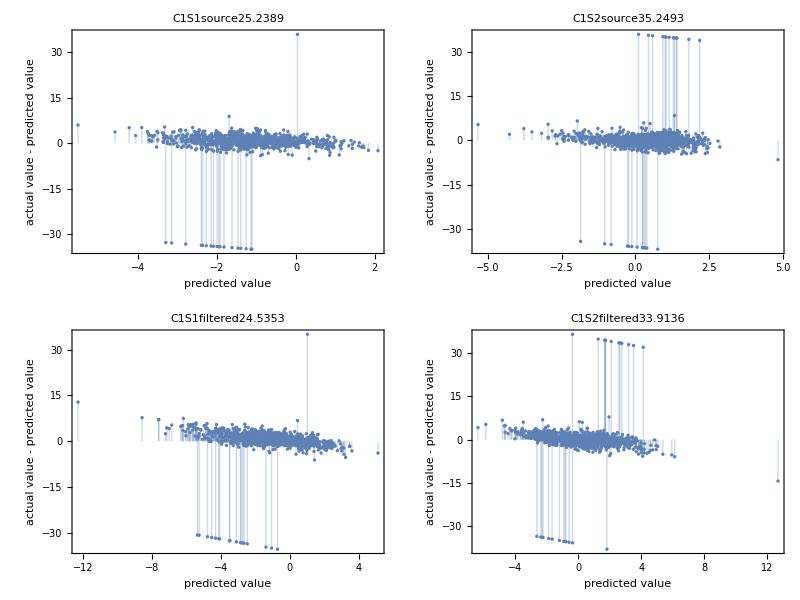

```mathematica
Grid[Table[plot[pm,label,type],{type,{"source","filtered"}},{label,{"C1S1","C1S2"}}]]
```

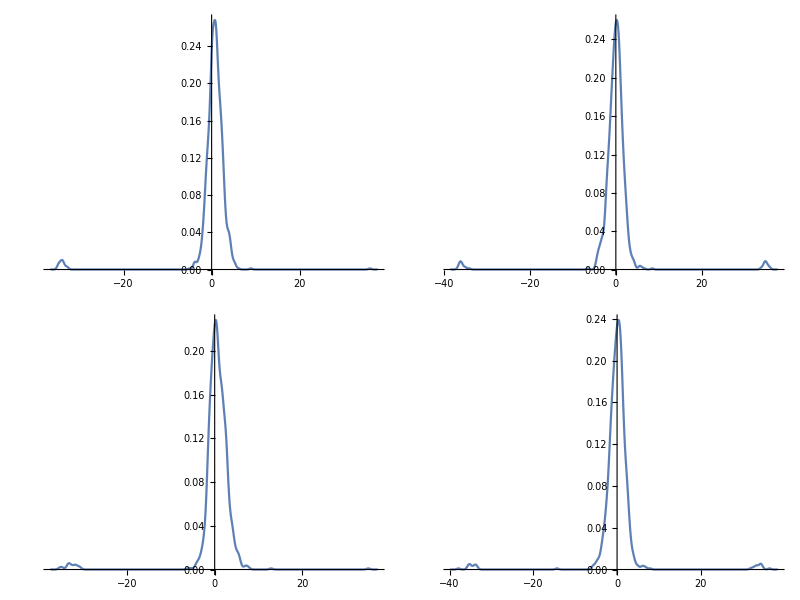

```mathematica
Grid[Table[smPlot[pm,label,type],{type,{"source","filtered"}},{label,{"C1S1","C1S2"}}]]
```

```mathematica
pm["C1S1","source"]["MeanSquare"]
pm["C1S2","source"]["MeanSquare"]
```

25.2389

35.2493

```mathematica
pm["C1S1","filtered"]["MeanSquare"]
pm["C1S2","filtered"]["MeanSquare"]
```

24.5353

33.9136

```mathematica
ByteCount[predict["C1S1"]]
ByteCount[predict["C1S2"]]
```

869480

3749984

```mathematica
sigmoid[x_]:=1/(1+E^-x)
```

```mathematica
id=RandomChoice[allKeys];
loadImage[id,256]
img=loadImage[id,32];
Row[{predict["C1S1"][img],Spacer[20],predict["C1S2"][img]}]
Row[Riffle[Values[Normal[$TrainingDataByID[SelectFirst[#GalaxyID==id&],{"C1S1","C1S2"}]]],Spacer[20]]]
```

-Graphics-

-1.283361.04984

-1.129131.12913

```mathematica
p[img]
```

-4.56488

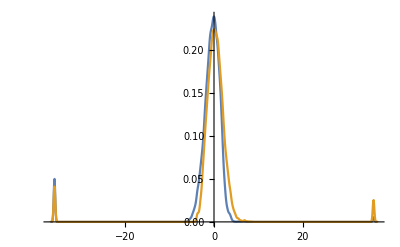

```mathematica
SmoothHistogram[Normal[$TrainingDataByID[All,#]]&/@$VariableNames⟦2;;3⟧,PlotRange->All]
```

```mathematica
threshold=5;
weird=Normal[$TrainingDataByID[Select[#C1S1<threshold&&#C1S2>threshold&&#C1S3<threshold&],"GalaxyID"]];
Length[weird]
```

1078

```mathematica
Export["C:\\Users\\rhennigan\\Desktop\\galaxiesS.jpg",ImageAssemble[Partition[ImageResize[Import[FileNameJoin[{$GalaxyImageSourceDirectory,ToString[#]<>".jpg"}]],128]&/@weird,Sqrt[Length[weird]]//Round]]]
```

C:\Users\rhennigan\Desktop\galaxiesS.jpg

```mathematica
Export["C:\\Users\\rhennigan\\Desktop\\galaxiesF.jpg",ImageAssemble[Partition[ImageResize[Import[FileNameJoin[{$GalaxyImageFilteredDirectory,ToString[#]<>".jpg"}]],128]&/@weird,Sqrt[Length[weird]]//Round]]]
```

C:\Users\rhennigan\Desktop\galaxiesF.jpg

```mathematica
id=RandomChoice[weird]
Import[FileNameJoin[{$GalaxyImageFilteredDirectory,ToString[id]<>".jpg"}]]
$TrainingDataByID[Select[#GalaxyID==id&]]
```

839801

-Graphics-

```mathematica
SmoothHistogram[Values[$TrainingDataByID⟦All,"Class1.1"⟧]]
```

<|100008→-0.297226,100023→-0.44821,100053→0.724814,100078→0.505445,100090→1.50501,100122→0.639749,100123→-0.0941576,100128→0.489576,100134→-2.01726,100143→-0.613288,100150→-0.177958,100157→-0.438638,100187→-0.129399,100204→-0.0812414,100237→-0.97657,100259→-0.416295,100263→-0.916684,100288→0.373414,100295→0.651447,100322→-1.32862,100335→-0.974106,100367→-0.0716782,100380→-1.88079,100382→-0.653053,100383→-0.509217,100402→0.279319,100428→0.568909,100434→0.668209,100444→0.810254,100445→-0.890521,100458→0.918831,100474→-0.836574|>

```mathematica
variableNames
```

{GalaxyID,Class1.1,Class1.2,Class1.3,Class2.1,Class2.2,Class3.1,Class3.2,Class4.1,Class4.2,Class5.1,Class5.2,Class5.3,Class5.4,Class6.1,Class6.2,Class7.1,Class7.2,Class7.3,Class8.1,Class8.2,Class8.3,Class8.4,Class8.5,Class8.6,Class8.7,Class9.1,Class9.2,Class9.3,Class10.1,Class10.2,Class10.3,Class11.1,Class11.2,Class11.3,Class11.4,Class11.5,Class11.6}

```mathematica
row=RandomChoice[data]
```

{678584,0.816875,0.183125,0,0,0.183125,0,0.183125,0,0.183125,0.0542268,0.0887114,0.0401868,0,0.064045,0.935955,0.801002,0.0158727,0,0,0,0.064045,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

<|Class1.1→0.816875,Class1.2→0.183125,Class1.3→0.,Class2.1→0.,Class2.2→0.183125,Class3.1→0.,Class3.2→0.183125,Class4.1→0.,Class4.2→0.183125,Class5.1→0.0542268,Class5.2→0.0887114,Class5.3→0.0401868,Class5.4→0.,Class6.1→0.064045,Class6.2→0.935955,Class7.1→0.801002,Class7.2→0.0158727,Class7.3→0.,Class8.1→0.,Class8.2→0.,Class8.3→0.064045,Class8.4→0.,Class8.5→0.,Class8.6→0.,Class8.7→0.,Class9.1→0.,Class9.2→0.,Class9.3→0.,Class10.1→0.,Class10.2→0.,Class10.3→0.,Class11.1→0.,Class11.2→0.,Class11.3→0.,Class11.4→0.,Class11.5→0.,Class11.6→0.|>

678584→<|Class1.1→0.816875,Class1.2→0.183125,Class1.3→0.,Class2.1→0.,Class2.2→0.183125,Class3.1→0.,Class3.2→0.183125,Class4.1→0.,Class4.2→0.183125,Class5.1→0.0542268,Class5.2→0.0887114,Class5.3→0.0401868,Class5.4→0.,Class6.1→0.064045,Class6.2→0.935955,Class7.1→0.801002,Class7.2→0.0158727,Class7.3→0.,Class8.1→0.,Class8.2→0.,Class8.3→0.064045,Class8.4→0.,Class8.5→0.,Class8.6→0.,Class8.7→0.,Class9.1→0.,Class9.2→0.,Class9.3→0.,Class10.1→0.,Class10.2→0.,Class10.3→0.,Class11.1→0.,Class11.2→0.,Class11.3→0.,Class11.4→0.,Class11.5→0.,Class11.6→0.|>

```mathematica
img=Import[RandomChoice[filteredImageFileNames]]
```

-Graphics-

```mathematica
ByteCount[img]
```

135272

```mathematica
n=1000;
images=Import/@filteredImageFileNames⟦;;n⟧;
```

```mathematica
ByteCount[images]
```

135280200

```mathematica
ByteCount/@images//First
```

135272

```mathematica
filteredImageFileNames//Length
```

61578

```mathematica
UnitConvert[Quantity[135272*61578,"bytes"],"GB"]//QuantityMagnitude
```

520611201/62500000

```mathematica
%//N
```

8.32978